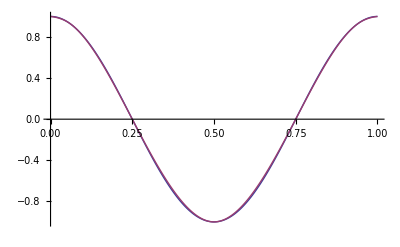

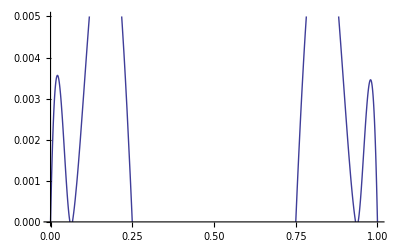

```mathematica
n=6;
Do[x[k]=(Sin[(k*Pi)/(2*n)])^2,{k,0,n}];(*vuzlite *)
f[t_]:= Cos[2*Pi*t]; 
Do[h[k]=x[k+1]-x[k],{k,0,n-1}]; (* delta *)
Do[ d[k]=f[x[k]],{k,0,n}]; (* fk *)

(* progonkata *) 
Do[cb[k]=2/h[k-1]+2/h[k],{k,1,n-1}];
Do[ca[k]=1/h[k-1],{k,2,n-1}];
Do[cc[k]=1/h[k],{k,1,n-2}];
Do[val[k]=3*(d[k]-d[k-1])/h[k-1]^2+3*(d[k+1]-d[k])/h[k]^2,{k,1,n-1}];


alpha[1]=-cc[1]/cb[1];
beta[1]=val[1]/cb[1];
Do[alpha[k]=-cc[k]/(ca[k]*alpha[k-1]+cb[k]),{k,2,n-2}];
Do[beta[k]=(val[k]-ca[k]*beta[k-1])/(ca[k]*alpha[k-1]+cb[k]),{k,2,n-1}];


c[0] = 3*(d[1] - d[0])/2*h[1] - c[1]/2;
c[n] = 3*(d[n] - d[n-1])/2*h[n] - c[n-1]/2;
c[n-1]=beta[n-1];
For[k=n-2,k>0,k--,c[k]=alpha[k]*c[k+1]+beta[k]];

Do[b[k]=(d[k+1]-d[k])/h[k]^2-c[k]/h[k],{k,0,n-1}];
Do[a[k]=c[k+1]/h[k]^2+c[k]/h[k]^2+2*(d[k]-d[k+1])/h[k]^3,{k,0,n-1}];
Do[sp[k,z_]=a[k]*(z-x[k])^2*(z-x[k+1])+b[k]*(z-x[k])^2+c[k]*(z-x[k])+d[k],{k,0,n-1}];

helper[i_,t_]:=If[i≤n+1,If[t≥x[i]&&t≤x[i+1],sp[i,t],helper[i+1,t]]];
s[t_]:=helper[0,t];

Plot[{f[t],s[t]}, {t, 0, 1}, PlotPoints->200]

Plot[f[t]-s[t] , {t, 0, 1}, PlotRange->{0,0.005}]
```